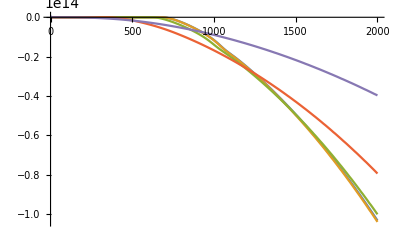
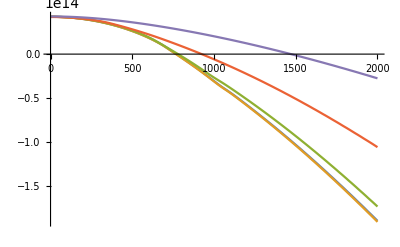
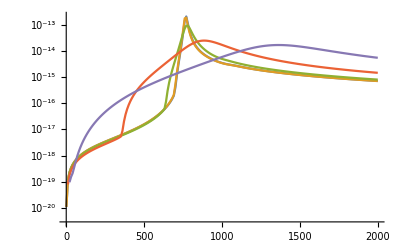

```mathematica
SetDirectory[NotebookDirectory[]];
Tall={1,50,100,150,200};
omegaall=Table[Flatten[Import["./mub0T"<>ToString[Tall[[i]]]<>"/buffer/omega.dat"]],{i,1,Length[Tall]}];
Impartall=Table[Flatten[Import["./mub0T"<>ToString[Tall[[i]]]<>"/buffer/Im.dat"]],{i,1,Length[Tall]}];
Repartall=Table[Flatten[Import["./mub0T"<>ToString[Tall[[i]]]<>"/buffer/Re.dat"]],{i,1,Length[Tall]}];
mrhoall=Table[Flatten[Import["./mub0T"<>ToString[Tall[[i]]]<>"/buffer/mrho2bare.dat"]],{i,1,Length[Tall]}];
rhoall=-1/π*Impartall/((Repartall+mrhoall)^2+Impartall^2);
plot=ListLinePlot[Table[Transpose[{omegaall[[i]],Impartall[[i]]}],{i,1,Length[Tall]}],PlotRange->All];
plot2=ListLinePlot[Table[Transpose[{omegaall[[i]],Repartall[[i]]+mrhoall[[i]]}],{i,1,Length[Tall]}],PlotRange->All];
plot3=ListLinePlot[Table[Transpose[{omegaall[[i]],rhoall[[i]]}],{i,1,Length[Tall]}],PlotRange->All,ScalingFunctions->{Automatic,"Log"}];
{plot,plot2,plot3}
```

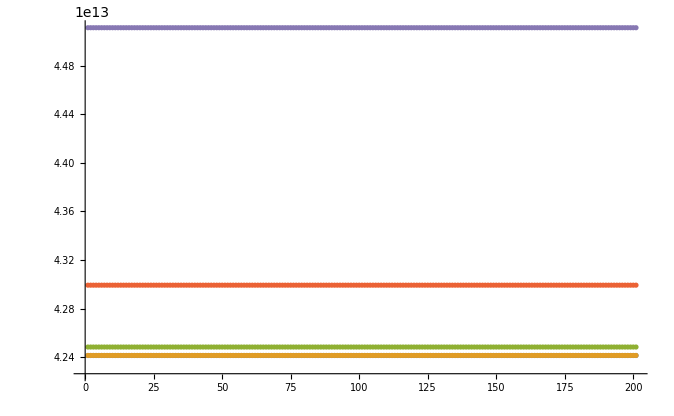

```mathematica
ListPlot[mrhoall]
```